# Regression modelling, multiple outputs

```mathematica
(* column vectorize/unvectorize, following Magnus, 1999 *)
f1 =Length@X;
f2=Length@Y;
tocolumn[c_]:=Transpose[{c}] (* turns vector to column matrix *)
vectorize[W_]:=Transpose@{Flatten@Transpose[W]};
unvectorize[Wf_]:=Transpose[Flatten/@Partition[Wf,f2]];
errf[Wf_]:=(unvectorize[Wf].X-Y);
lossf[Wf_]:=Tr[errf[Wf].errf[Wf]ᵀ/dsize]
gradf[Wf_]:=vectorize@grad@unvectorize@Wf;
```

```mathematica
(* Batch dimension is last one *)
n=2;
e=0.01;
trueCov={{1, 1-e},{1-e,1}};
zero=0&/@Range@n;
normal=MultinormalDistribution[zero,trueCov];
pdf[x_,y_]=PDF[normal,{x,y}];
dsize=10;
SeedRandom[0];
X=RandomVariate[normal,{dsize}]//Transpose;
(* center the data *)
Xc=Mean[Transpose@X];
X=Transpose[#-Xc&/@Transpose[X]];
Wt = {{1,1},{1,-1}}; (* |true w *)
Wtf=vectorize[Wt];
W0={{2,1},{0,0}}; (* initial w *)
W0f=vectorize[W0];
Y=Dot[Wt, X];
XY = X~Join~Y;
grad[W_]:=2(W.X-Y).Transpose[X]/dsize;
err[W_]:=(W.X-Y);
loss[W_]:=Tr[err[W].err[W]ᵀ/dsize];
Print["Loss at W0 ",loss[W0]];
Print["Grad at w0 ",grad[W0]];
cov=X.Xᵀ/dsize; 
(* sanity checks *)
Print["True cov ",MatrixForm@trueCov];
Print["Data cov ", MatrixForm@cov];
Print["Data mean ", Mean@Transpose@X];
```

Loss at W0 0.459117

Grad at w0 {{0.890809,0.89192},{0.00111117,0.0285363}}

True cov (1 | 0.99
0.99 | 1)

Data cov (0.445404 | 0.44596
0.44596 | 0.460228)

Data mean {4.996×10^-17,-1.11022×10^-17}

```mathematica
Y.Xᵀ.PseudoInverse[X.Xᵀ]-Wt//Chop//MatrixForm
```

(0 | 0
0 | 0)

## Symbolic Hessian

```mathematica
Clear[v];
var=Array[v,{f2,f1}];
varf=vectorize@var;
sub[v_]:=Thread[Flatten@var->Flatten@v]
lossf[varf]/.sub[W0]
```

0.459117

```mathematica
lossf@varf/.sub[W0]
```

0.459117

```mathematica
D[lossf[varf],{Flatten[varf],1}]/.sub[W0]//MatrixForm
```

(0.890809
0.00111117
0.89192
0.0285363)

```mathematica
grad[W0]//MatrixForm
```

(0.890809 | 0.89192
0.00111117 | 0.0285363)

```mathematica
tocolumn[(D[lossf[varf],{Flatten[varf],1}]/.sub[W0])]
```

{{0.890809},{0.00111117},{0.89192},{0.0285363}}

```mathematica
tocolumn[D[lossf[varf],{Flatten[varf],1}]/.sub[W0]]==vectorize[grad[W0]]
```

True

```mathematica
D[lossf[varf],{Flatten[varf],2}]//MatrixForm
```

(0.890809 | 0 | 0.89192 | 0
0 | 0.890809 | 0 | 0.89192
0.89192 | 0 | 0.920456 | 0
0 | 0.89192 | 0 | 0.920456)

```mathematica
KroneckerProduct[grad[W0],IdentityMatrix@2]-D[lossf[varf],{Flatten[varf],2}]//Chop//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
-0.890809 | 0 | -0.89192 | 0
0 | -0.890809 | 0 | -0.89192)

```mathematica
2X.Xᵀ/dsize//MatrixForm
```

(0.890809 | 0.89192
0.89192 | 0.920456)

```mathematica
D[Tr[varᵀ.Array[a,{2,2}].var],{Flatten@vectorize@var,2}]//MatrixForm
```

(2 a[1,1] | a[1,2]+a[2,1] | 0 | 0
a[1,2]+a[2,1] | 2 a[2,2] | 0 | 0
0 | 0 | 2 a[1,1] | a[1,2]+a[2,1]
0 | 0 | a[1,2]+a[2,1] | 2 a[2,2])

```mathematica
KroneckerProduct[IdentityMatrix@2,2X.Xᵀ/dsize]//MatrixForm
```

(0.890809 | 0.89192 | 0. | 0.
0.89192 | 0.920456 | 0. | 0.
0. | 0. | 0.890809 | 0.89192
0. | 0. | 0.89192 | 0.920456)

```mathematica
vectorize[KroneckerProduct[IdentityMatrix@2,2X.Xᵀ/dsize]]
```

{{0.890809},{0.89192},{0.},{0.},{0.89192},{0.920456},{0.},{0.},{0.},{0.},{0.890809},{0.89192},{0.},{0.},{0.89192},{0.920456}}

```mathematica
KroneckerProduct[2X.Xᵀ/dsize,IdentityMatrix@2]//MatrixForm
```

(0.890809 | 0. | 0.89192 | 0.
0. | 0.890809 | 0. | 0.89192
0.89192 | 0. | 0.920456 | 0.
0. | 0.89192 | 0. | 0.920456)

## Optimize

```mathematica
(* since our gradients are column vectors, pre-condition multiply on left *)
(* takes loss, grad, learning rate, produces list of losses *)
(* globals: points *)
optimizef[loss_,grad_,w0_,pre_,lr_]:=Module[{gradstep},
gradstep[w_]:=w-lr*pre.grad[w];
points=NestList[gradstep,w0,50];
loss/@points
];
```

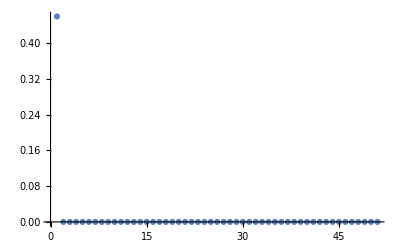

```mathematica
hess=KroneckerProduct[2X.Xᵀ/dsize,IdentityMatrix@2];
pre=Inverse@hess;
ListPlot[optimizef[lossf,gradf,W0f,pre,1.],PlotRange->All]
```